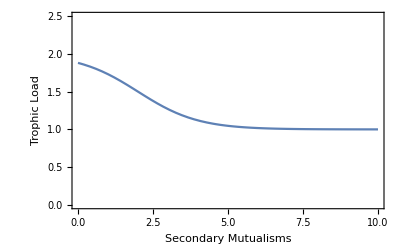

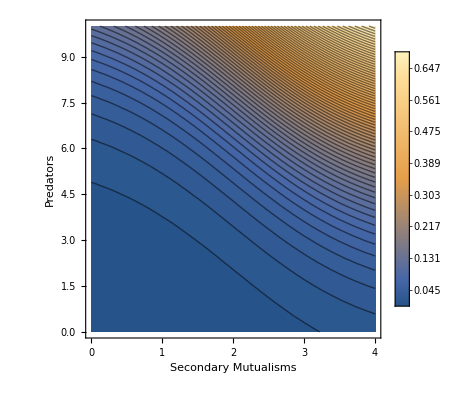

```mathematica
trophicload = mintl+1/(1/(dtl-mintl)+1Exp[secmut-dtl]);
Plot[trophicload/.{dtl->2,mintl->1},{secmut,0,10},PlotRange->{0,2.5},Frame->True,FrameLabel->{"Secondary Mutualisms","Trophic Load"}]
prext=(1/(1+Exp[-0.5*(prednum-(trophicload*(gL/gS)))]));
ContourPlot[prext/.{dtl->2,mintl->1,gL->3000,gS->400},{secmut,0,4},{prednum,0,10},FrameLabel->{"Secondary Mutualisms","Predators"},PlotLegends->Table[x,{x,0,1,0.001}],Contours->100,PlotRange->{0,1}]
```

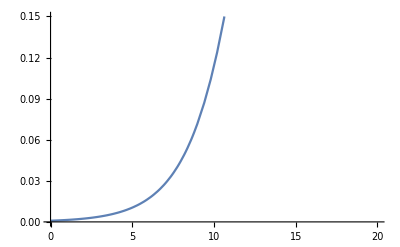

```mathematica
Plot[prext/.{gL->3000,gS->400,mintl->1,dtl->2,secmut->0},{prednum,0,20},PlotRange->{0,0.15}]
```